```mathematica
Needs["Combinatorica`"]
```

```mathematica
Sum[1/((z-2)!),{z,1,N}]
```

(ⅇ Gamma[N,1])/Gamma[N]

```mathematica
Sum[1/((z-1)!)*(1/(N-z)!),{z,1,N}]
```

2^(-1+N)/((-1+N)!)

```mathematica
Limit[2^N/(N!),N->Infinity]
```

0

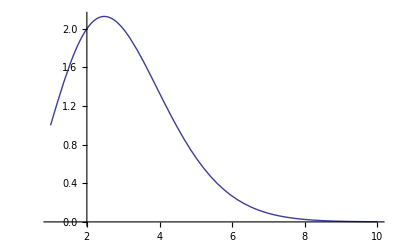

```mathematica
Plot[2^(x-1)/Gamma[x],{x,1,10}]
```

```mathematica
2^(10)/(10!)//N
```

0.000282187

```mathematica
Sum[z/((z-1)!),{z,1,N}]
```

(ⅇ Gamma[1+N] ((1+N) Gamma[N,1]-Gamma[1+N,1])+Gamma[N] (-1+ⅇ Gamma[1+N,1]))/(Gamma[N] Gamma[1+N])

```mathematica
Limit[Gamma[N,1]/Gamma[N],N->Infinity]
```

1

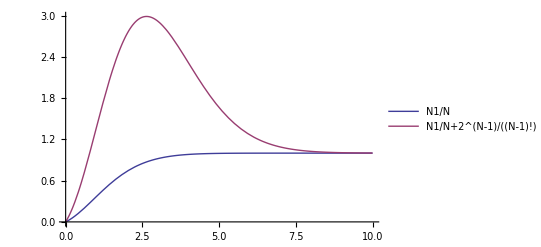

```mathematica
Plot[{Gamma[N,1]/Gamma[N],Gamma[N,1]/Gamma[N]+2^(N-1)/((N-1)!)},{N,0,10},PlotLegends->LineLegend["Expressions"]]
```

```mathematica
NumberOfDerangements[0]
```

1

```mathematica
f[N_]:= Sum[k*(1/N!)*Binomial[N,k]*NumberOfDerangements[N-k],{k,0,N}]
```

```mathematica
Data={{1,f[1]},{2,f[2]}}
```

{{1,1},{2,1}}

```mathematica
Graphics[{PointSize[Medium],Blue,Point[Data]}]
```

```mathematica
Table[{k,f[k]},{k,1,10}]
```

{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1}}

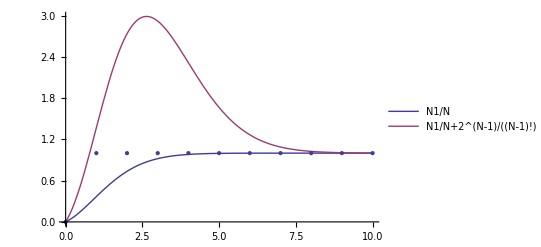

```mathematica
Show[Plot[{Gamma[N,1]/Gamma[N],Gamma[N,1]/Gamma[N]+2^(N-1)/((N-1)!)},{N,0,10},PlotLegends->LineLegend["Expressions"]],ListPlot[Table[{k,f[k]},{k,0,10}]]]
```

```mathematica
Gamma[10,1]//N
```

362880.

```mathematica
Gamma[10]
```

362880

```mathematica
Table[{k,f[k]},{k,1,50}]
```

{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1},{11,1},{12,1},{13,1},{14,1},{15,1},{16,1},{17,1},{18,1},{19,1},{20,1},{21,1},{22,1},{23,1},{24,1},{25,1},{26,1},{27,1},{28,1},{29,1},{30,1},{31,1},{32,1},{33,1},{34,1},{35,1},{36,1},{37,1},{38,1},{39,1},{40,1},{41,1},{42,1},{43,1},{44,1},{45,1},{46,1},{47,1},{48,1},{49,1},{50,1}}

```mathematica
g[n_]:=Sum[k^2*(1/n!)*Binomial[n,k]*(n-k)!/Exp[1],{k,0,n}]//N
```

```mathematica
Table[{k,g[k]},{k,1,50}]
```

{{1,0.367879},{2,1.10364},{3,1.65546},{4,1.90071},{5,1.97735},{6,1.99575},{7,1.99932},{8,1.99991},{9,1.99999},{10,2.},{11,2.},{12,2.},{13,2.},{14,2.},{15,2.},{16,2.},{17,2.},{18,2.},{19,2.},{20,2.},{21,2.},{22,2.},{23,2.},{24,2.},{25,2.},{26,2.},{27,2.},{28,2.},{29,2.},{30,2.},{31,2.},{32,2.},{33,2.},{34,2.},{35,2.},{36,2.},{37,2.},{38,2.},{39,2.},{40,2.},{41,2.},{42,2.},{43,2.},{44,2.},{45,2.},{46,2.},{47,2.},{48,2.},{49,2.},{50,2.}}